## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.03;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataG=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/41/tables/geyger.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataG//TableForm
```

№ | x | N' | t | N |  | 
1. | 10. | 1104. | 74.9 | 14.74 | 0.44 | 0.5
2. | 13. | 1167. | 75.1 | 15.54 | 0.45 | 0.5
3. | 15. | 1175. | 75. | 15.67 | 0.46 | 0.5
4. | 16. | 1146. | 74.9 | 15.3 | 0.45 | 0.5
5. | 17. | 659. | 74.7 | 8.82 | 0.34 | 0.5
6. | 18. | 134. | 75. | 1.79 | 0.15 | 0.5
7. | 19. | 39. | 74.9 | 0.52 | 0.08 | 0.5
8. | 20. | 34. | 74.3 | 0.46 | 0.08 | 0.5
9. | 22. | 18. | 74.9 | 0.24 | 0.06 | 0.5
10. | 25. | 19. | 75.2 | 0.25 | 0.06 | 0.5
11. | 30. | 12. | 74.7 | 0.16 | 0.05 | 0.5
12. | 35. | 14. | 74.7 | 0.19 | 0.05 | 0.5
13. | 40. | 13. | 74.9 | 0.17 | 0.05 | 0.5

```mathematica
dataGf=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/41/tables/gfit.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataGf//TableForm
```

№ | x | N' | t | N |  | 
4. | 16. | 1146. | 74.9 | 15.3 | 0.45 | 0.5
5. | 17. | 659. | 74.7 | 8.82 | 0.34 | 0.5
6. | 18. | 134. | 75. | 1.79 | 0.15 | 0.5
7. | 19. | 39. | 74.9 | 0.52 | 0.08 | 0.5

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitG=dataGf⟦2;;,{2,5}⟧;
fitG=LinearModelFit[forFitG,{1,x},x]
fitG@"ParameterTable"
Plot[fitG["Function"]@x, {x, 0, 32}]
```

FittedModel[96.505-5.137 x]

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 96.50500000000062, 16.ffrfr4283, 5.874330969648964, 0.027777220512164247}, {x, -5.137000000000035, 0.9368473728414889, -5.483283775904015, 0.031687333121834804}}
```

```mathematica
{{"", "Estimate", "Standard Error"}, {1, 96.50500000000062, 16.42825378730193}, {x, -5.137000000000035, 0.9368473728414889}}
```

{{,Estimate,Standard Error},{1,96.505,16.4283},{x,-5.137,0.936847}}

```mathematica
(5.137000000000035/96.50500000000062)^-1
```

```mathematica
18.78625656998247*0.24947685834206293
```

4.68674

```mathematica
Sqrt[(16.42825378730193/96.5050000000006)^2+(0.9368473728414889/5.137000000000035)^2]
```

0.249477

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,96.50500000000062,16.42825378730193},{x,-5.137000000000035,0.9368473728414889}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 96.505 & 16.4283 \\
 x & -5.137 & 0.936847 \\
\end{array}
\right)

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

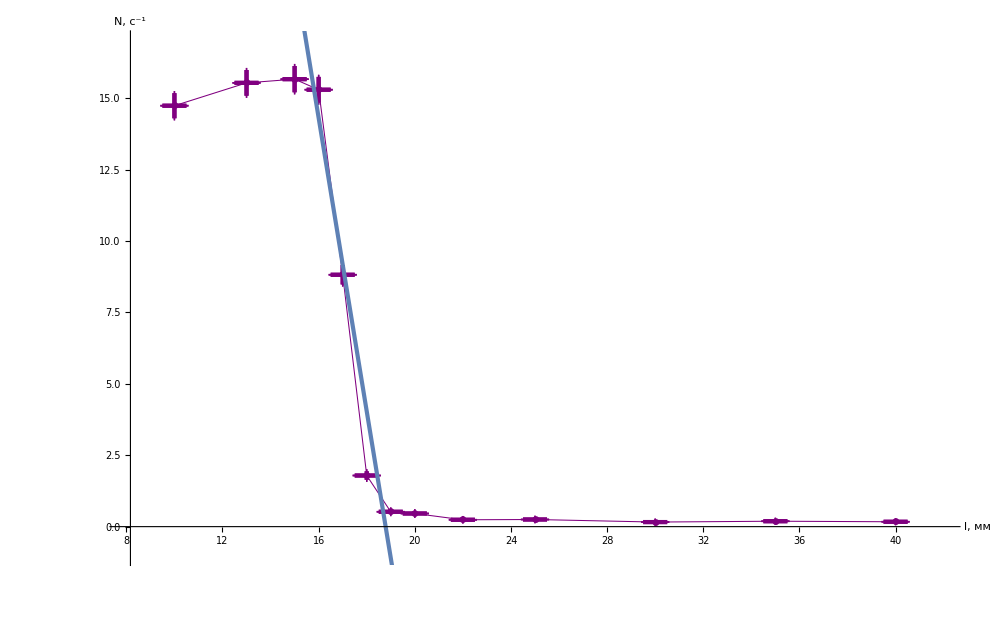

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@Sort[dataG⟦2;;,{2,5,7,6}⟧],
GridLines->{grids@1,grids@1},
Joined->True,
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"l, мм","N, (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> {Purple, Thickness@0.00075},ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{8,42},{-1,17}}], 
Plot[fitG["Function"]@x,{x,0,100}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXG=MapAt[dropLastDot@*ToString,dataG,{{2;;,All}}];
forTeXG//TeXForm
```

\left(
\begin{array}{cccccc}
 \unicode{2116} & \text{x} & \text{N'} & \text{t} & \text{N} & \text{} \\
 1 & 10 & 1104 & 74.9 & 14.74 & 0.44 \\
 2 & 13 & 1167 & 75.1 & 15.54 & 0.45 \\
 3 & 15 & 1175 & 75 & 15.67 & 0.46 \\
 4 & 16 & 1146 & 74.9 & 15.3 & 0.45 \\
 5 & 17 & 659 & 74.7 & 8.82 & 0.34 \\
 6 & 18 & 134 & 75 & 1.79 & 0.15 \\
 7 & 19 & 39 & 74.9 & 0.52 & 0.08 \\
 8 & 20 & 34 & 74.3 & 0.46 & 0.08 \\
 9 & 22 & 18 & 74.9 & 0.24 & 0.06 \\
 10 & 25 & 19 & 75.2 & 0.25 & 0.06 \\
 11 & 30 & 12 & 74.7 & 0.16 & 0.05 \\
 12 & 35 & 14 & 74.7 & 0.19 & 0.05 \\
 13 & 40 & 13 & 74.9 & 0.17 & 0.05 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/41/tables/Ion.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI//TableForm
```

```mathematica
dataI1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/41/tables/ion1.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI1//TableForm
```

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-49.0842+1.6875 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -49.0842 | 7.94615 | -6.1771 | 0.0000474773
x | 1.6875 | 0.0254062 | 66.4207 | 8.99885×10^-17

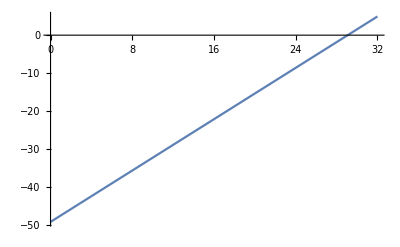

```mathematica
forFitI1=dataI1⟦2;;,{2,3}⟧;
fitI1=LinearModelFit[forFitI1,{1,x},x]
fitI1@"ParameterTable"
Plot[fitI1["Function"]@x, {x, 0, 32}]
```

```mathematica
dataI2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/41/tables/ion2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI2//TableForm
```

n | p | а
18. | 561. | 859.
19. | 581. | 858.
20. | 601. | 859.
21. | 611. | 861.
22. | 631. | 854.
23. | 641. | 860.
24. | 651. | 857.
25. | 671. | 860.
15. | 516. | 823.
16. | 536. | 850.
17. | 546. | 862.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitI2=dataI2⟦2;;,{2,3}⟧;
fitI2=LinearModelFit[forFitI2,{1,x},x]
fitI2@"ParameterTable"
Plot[fitI2["Function"]@x, {x, 0, 32}]
```

FittedModel[860.443-0.00314136 x]

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 860.4429319371873, 15.068696907513411, 57.10134971977314, 1.9378920016412194*^-9}, {x, -0.003141361256567945, 0.024325368354661113, -0.1291393088387092, 0.9014676607577486}}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

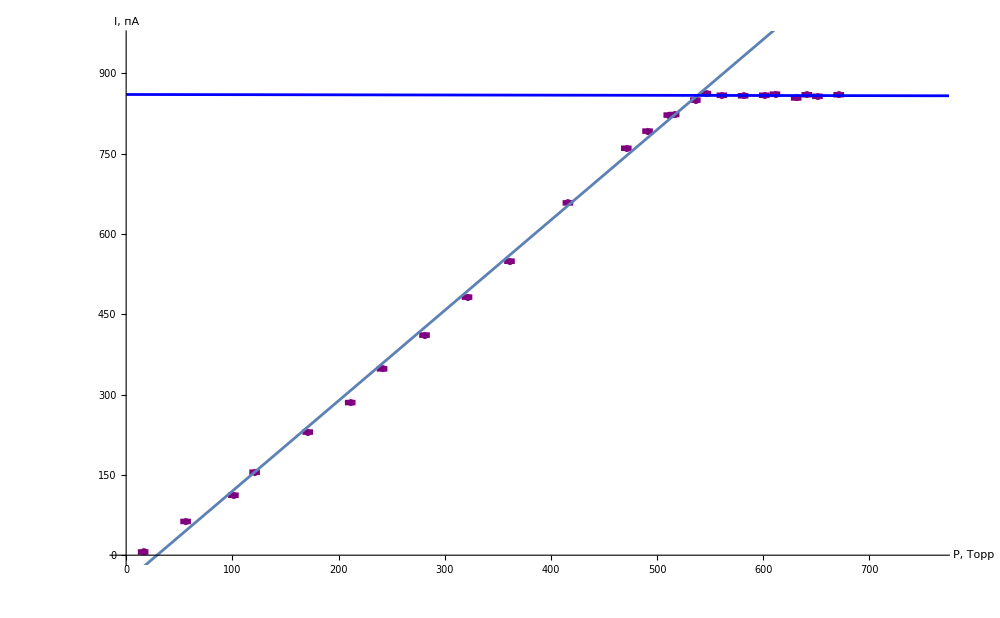

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI⟦2;;,{4,3,5,6}⟧,
GridLines->{grids@50,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"P, Торр","I, пА"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,760},{0,960}}], 
Plot[fitI1["Function"]@x,{x,0,1000}, PlotStyle->Thickness@0.002], 
Plot[fitI2["Function"]@x,{x,0,1000}, PlotStyle->{Thickness@0.002, Blue}]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXI2=MapAt[dropLastDot@*ToString,dataI2,{{2;;,All}}];
forTeXI2//TeXForm
```

\left(
\begin{array}{ccc}
 \text{n} & \text{p} & \unicode{0430} \\
 18 & 561 & 859 \\
 19 & 581 & 858 \\
 20 & 601 & 859 \\
 21 & 611 & 861 \\
 22 & 631 & 854 \\
 23 & 641 & 860 \\
 24 & 651 & 857 \\
 25 & 671 & 860 \\
 15 & 516 & 823 \\
 16 & 536 & 850 \\
 17 & 546 & 862 \\
\end{array}
\right)

```mathematica
Solve[860.4429319371873-0.003141361256567945* x==-49.08416094210012+1.6874975466143278*x,x]
```

{{x→537.978}}

```mathematica
(15+7.9)/(860.4429319371873+49.08416094210012)
```

0.0251779

```mathematica
(0.024325368354661113+0.02540620693523172)/(0.003141361256567945+1.6874975466143278)
```

0.0294158

```mathematica
Sqrt[0.025177919579619703^2+0.02941584690755889^2]
```

```mathematica
0.03871975831079966*537.9783279829394
```

20.8304

```mathematica
(537*288)/(760*298)
```

9666/14155

```mathematica
N[9666/14155]
```

```mathematica
0.6828682444365949*5
```

3.41434

```mathematica
N[336/505]
```

```mathematica
0.6653465346534654*5
```

3.32673

```mathematica
N[707/960]
```

0.736458

```mathematica
N[1043/1515]
```

```mathematica
0.6884488448844884*5
```

3.44224

```mathematica
N[40081/54720]
```

```mathematica
0.7324744152046784*5
```

3.66237